# Dalitz plots for HNL decay to three leptons

## Using FeynCalc and the SM_heavyN model (using only a single HNL)

## Preamble

```mathematica
description="N->νll Dalitz Plots";
```

```mathematica
IncludeTests = False;
```

### Importing FeynCalc

```mathematica
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose = 0;

FCCheckVersion[9,3,1];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

F::shdw: Symbol F appears in multiple contexts {FeynArts`,Global`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

G::shdw: Symbol G appears in multiple contexts {FeynArts`,Global`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

FeynArts 3.11 (3 Aug 2020) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

### Patching generated FeynArts models for use with FeynCalc

```mathematica
FAPatch[PatchModelsOnly->True];
```

## Calculating Squared Amplitudes

### Misc functions

```mathematica
ConvertDiagsToAmp[diags_]:= FCFAConvert[CreateFeynAmp[diags], IncomingMomenta->{p},OutgoingMomenta->{p1,-p2,p3},UndoChiralSplittings->True,ChangeDimension->4,List->False, SMP->True, Contract->True,FinalSubstitutions->{SMP["e"]->Sqrt[8/Sqrt[2]*SMP["G_F"]*SMP["m_W"]^2 SMP["sin_W"]^2],sw->SMP["sin_W"],cw->SMP["cos_W"],VeN1->VαN,mN1->mN,Me->SMP["m_e"],MMu->SMP["m_mu"]}]
```

```mathematica
ConvertToFermiAmp[amp_,pz_:p1-p2,pw_:p1-p3]:=Module[{Zpart,Wpart},
Zpart = SelectNotFree[amp,SMP["m_Z"]];
Wpart = SelectFree[amp,SMP["m_Z"]];
If[Zpart==1,Zpart=0];
If[Wpart==1,Wpart=0];
Zpart/(SMP["m_W"]^2/(1-SMP["sin_W"]^2)FeynAmpDenominator[PropagatorDenominator[Momentum[pz],SMP["m_Z"]]]) + Wpart/(SMP["m_W"]^2 FeynAmpDenominator[PropagatorDenominator[Momentum[pw],SMP["m_W"]]] )
]
```

```mathematica
SquareAmp[amp_]:= ReplaceAll[(amp (ComplexConjugate[amp, Conjugate->{VαN}]))//
	FeynAmpDenominatorExplicit//FermionSpinSum[#, ExtraFactor -> 1/2]&//DiracSimplify//Simplify,{VαN ComplexConjugate[VαN, Conjugate->{VαN}] -> Abs[VαN]^2}]/.{SMP["cos_W"]->Sqrt[1-SMP["sin_W"]^2]}//Simplify[#,Assumptions->{0<SMP["sin_W"]}]&;
```

## The case

by example of

### Generating Diagrams

```mathematica
diagsAAA = InsertFields[CreateTopologies[0, 1 -> 3], {F[13]} -> { +F[4],-F[4],F[1]}, InsertionLevel -> {Classes},Model -> FileNameJoin[{"SM_HeavyN","SM_HeavyN"}],GenericModel->FileNameJoin[{"SM_HeavyN","SM_HeavyN"}],ExcludeParticles-> {S[1],S[2],S[3],F[14],F[15]}];
Paint[diagsAAA, Numbering -> Simple, ColumnsXRows -> {2, 1},ImageSize->{512,256}];
```

-Graphics-

### Generating the Amplitude

#### Converting diagrams into amplitude

```mathematica
ampAAA[0] =ConvertDiagsToAmp[diagsAAA]
```

(2 √2 VαN G_F m_W^2 (φ(OverBar[p3])).(γ̄)^Lor2.(γ̄)^7.(φ(OverBar[p2],m_e)) (φ(OverBar[p1],m_e)).(γ̄)^Lor2.(γ̄)^7.(φ(p̄,mN)))/((OverBar[p3]-OverBar[p2])^2-m_W^2)+(ⅈ 2^(1/4) VαN √(G_F m_W^2 (sin(θ_W))^2) (φ(OverBar[p3])).(γ̄)^Lor1.(γ̄)^7.(φ(p̄,mN)) (φ(OverBar[p1],m_e)).((2 ⅈ 2^(1/4) (γ̄)^Lor1.(γ̄)^6 (sin(θ_W)) √(G_F m_W^2 (sin(θ_W))^2))/(cos(θ_W))-(ⅈ 2^(1/4) (γ̄)^Lor1.(γ̄)^7 (cos(θ_W)-sin(θ_W)) (cos(θ_W)+sin(θ_W)) √(G_F m_W^2 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p2],m_e)))/((cos(θ_W)) (sin(θ_W)) ((OverBar[p1]-OverBar[p2])^2-m_Z^2))

#### Switching to Fermi approximation and using generalised name scheme

```mathematica
FermiAmpAAA =ConvertToFermiAmp[ampAAA[0],p1-p2,p3-p2] /.{SMP["m_e"]->m2,Me->m2}
```

2 √2 VαN G_F (φ(OverBar[p3])).(γ̄)^Lor2.(γ̄)^7.(φ(OverBar[p2],m2)) (φ(OverBar[p1],m2)).(γ̄)^Lor2.(γ̄)^7.(φ(p̄,mN))+1/(m_W^2 (cos(θ_W)) (sin(θ_W)))ⅈ 2^(1/4) VαN (1-(sin(θ_W))^2) √(G_F m_W^2 (sin(θ_W))^2) (φ(OverBar[p3])).(γ̄)^Lor1.(γ̄)^7.(φ(p̄,mN)) (φ(OverBar[p1],m2)).((2 ⅈ 2^(1/4) (γ̄)^Lor1.(γ̄)^6 (sin(θ_W)) √(G_F m_W^2 (sin(θ_W))^2))/(cos(θ_W))-(ⅈ 2^(1/4) (γ̄)^Lor1.(γ̄)^7 (cos(θ_W)-sin(θ_W)) (cos(θ_W)+sin(θ_W)) √(G_F m_W^2 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p2],m2))

#### Declaring Kinematics

```mathematica
FCClearScalarProducts[]
Clear[m1,m2,m3]
m1 =m2; m3=0;
SP[p,p] =  mN^2;
SP[p1,p1] =m1^2;
SP[p2,p2] =m2^2;
SP[p3,p3] =m3^2;
SP[p,p1] =(m1^2+SP[p1,p2]+SP[p1,p3]);
SP[p,p2] =(SP[p1,p2]+m2^2+SP[p2,p3]);
SP[p,p3] =(SP[p1,p3]+SP[p2,p3]+m3^2);
SP[p1,p2] =1/2(M12sq-m1^2-m2^2);
SP[p2,p3] =1/2(M23sq-m2^2-m3^2);
SP[p1,p3] =1/2(mN^2+m2^2-M12sq-M23sq);
```

```mathematica
Clear[m1,m2,m3]
```

### Squared Average Amplitude

```mathematica
squareAmpAAA=ReplaceAll[SquareAmp[FermiAmpAAA]//Simplify[#,
Assumptions->{0<SMP["G_F"],0<SMP["m_e"],0<SMP["m_W"],0<SMP["m_Z"],0<M12sq,0<M23sq,0<mN}]&,{m2->ma}]
```

-1/(((sin(θ_W))^2-1)^2)4 Abs[VαN]^2 G_F^2 (((sin(θ_W))^2-1)^2 (sin(θ_W))^4 (M12sq^2-M12sq (-2 M23sq+6 ma^2+mN^2)+ma^2 (9 mN^2-10 M23sq)+5 M23sq (M23sq-mN^2)+5 ma^4)+2 ((sin(θ_W))^2-1) ((sin(θ_W))^4-1) (sin(θ_W))^2 (M12sq^2-M12sq (-2 M23sq+4 ma^2+mN^2)+ma^2 (3 mN^2-2 M23sq)+M23sq (M23sq-mN^2)+ma^4)+(M12sq+M23sq-ma^2) ((sin(θ_W))^4-1)^2 (M12sq+M23sq-ma^2-mN^2))

## The case

by example of

### Generating Diagrams

```mathematica
diagsBBA = InsertFields[CreateTopologies[0, 1 -> 3], {F[13]} -> {-F[5], +F[5],F[1]}, InsertionLevel -> {Classes},Model -> FileNameJoin[{"SM_HeavyN","SM_HeavyN"}],GenericModel->FileNameJoin[{"SM_HeavyN","SM_HeavyN"}],ExcludeParticles-> {S[1],S[2],S[3],F[14],F[15]}];
Paint[diagsBBA, Numbering -> Simple, ColumnsXRows -> {1, 1},ImageSize->{256,256}];
```

-Graphics-

### Generating the Amplitude

#### Converting diagrams into amplitude

```mathematica
ampBBA[0] =ConvertDiagsToAmp[diagsBBA]
```

-(ⅈ 2^(1/4) VαN √(G_F m_W^2 (sin(θ_W))^2) (φ(OverBar[p3])).(γ̄)^Lor1.(γ̄)^7.(φ(p̄,mN)) (φ(-OverBar[p2],MMU)).((2 ⅈ 2^(1/4) (γ̄)^Lor1.(γ̄)^6 (sin(θ_W)) √(G_F m_W^2 (sin(θ_W))^2))/(cos(θ_W))-(ⅈ 2^(1/4) (γ̄)^Lor1.(γ̄)^7 (cos(θ_W)-sin(θ_W)) (cos(θ_W)+sin(θ_W)) √(G_F m_W^2 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))).(φ(-OverBar[p1],MMU)))/((cos(θ_W)) (sin(θ_W)) ((OverBar[p1]-OverBar[p2])^2-m_Z^2))

#### Switching to Fermi approximation and using generalised name scheme

```mathematica
FermiAmpBBA = (ampBBA[0]/(SMP["m_W"]^2/(1-SMP["sin_W"]^2)FeynAmpDenominator[PropagatorDenominator[Momentum[p1-p2],SMP["m_Z"]]] ))/.{SMP["m_mu"]->m2,MMU->m2}
```

-1/(m_W^2 (cos(θ_W)) (sin(θ_W)))ⅈ 2^(1/4) VαN (1-(sin(θ_W))^2) √(G_F m_W^2 (sin(θ_W))^2) (φ(OverBar[p3])).(γ̄)^Lor1.(γ̄)^7.(φ(p̄,mN)) (φ(-OverBar[p2],m2)).((2 ⅈ 2^(1/4) (γ̄)^Lor1.(γ̄)^6 (sin(θ_W)) √(G_F m_W^2 (sin(θ_W))^2))/(cos(θ_W))-(ⅈ 2^(1/4) (γ̄)^Lor1.(γ̄)^7 (cos(θ_W)-sin(θ_W)) (cos(θ_W)+sin(θ_W)) √(G_F m_W^2 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))).(φ(-OverBar[p1],m2))

#### Declaring Kinematics

```mathematica
FCClearScalarProducts[]
Clear[m1,m2,m3]
m3=0;
m1=m2;
SP[p,p] =  mN^2;
SP[p1,p1] =m1^2;
SP[p2,p2] =m2^2;
SP[p3,p3] =m3^2;
SP[p,p1] =(m1^2+SP[p1,p2]+SP[p1,p3]);
SP[p,p2] =(SP[p1,p2]+m2^2+SP[p2,p3]);
SP[p,p3] =(SP[p1,p3]+SP[p2,p3]+m3^2);
SP[p1,p2] =1/2(M12sq-m1^2-m2^2);
SP[p2,p3] =1/2(M23sq-m2^2-m3^2);
SP[p1,p3] =1/2(mN^2+m2^2-M12sq-M23sq);
```

```mathematica
Clear[m1,m2,m3]
```

### Squared Average Amplitude

```mathematica
squareAmpBBA=SquareAmp[FermiAmpBBA]//Simplify[#,
Assumptions->{0<SMP["G_F"],0<SMP["m_e"],0<M12sq,0<M23sq,0<mN}]&//ReplaceAll[#,{m2->mb}]&
```

-4 Abs[VαN]^2 G_F^2 (4 (sin(θ_W))^4 (M12sq^2-M12sq (-2 M23sq+4 mb^2+mN^2)+2 (-2 mb^2 (M23sq-mN^2)+M23sq (M23sq-mN^2)+mb^4))+4 (sin(θ_W))^2 (M12sq mb^2+2 mb^2 (M23sq-mN^2)+M23sq (mN^2-M23sq)-mb^4)+mb^2 (mN^2-2 M23sq)+M23sq (M23sq-mN^2)+mb^4)

## The case

by example of

### Generating Diagrams

```mathematica
diagsABB = InsertFields[CreateTopologies[0, 1 -> 3], {F[13]} -> {F[4],-F[5],F[2]}, InsertionLevel -> {Classes},Model -> FileNameJoin[{"SM_HeavyN","SM_HeavyN"}],GenericModel->FileNameJoin[{"SM_HeavyN","SM_HeavyN"}],ExcludeParticles-> {S[1],S[2],S[3],F[14],F[15]}];
Paint[diagsABB, Numbering -> Simple, ColumnsXRows -> {1, 1},ImageSize->{256,256}];
```

-Graphics-

### Generating the Amplitudes

#### Converting diagrams into amplitude

```mathematica
ampABB[0] =ConvertDiagsToAmp[diagsABB]
```

(2 √2 VαN G_F m_W^2 (φ(OverBar[p3])).(γ̄)^Lor2.(γ̄)^7.(φ(OverBar[p2],MMU)) (φ(OverBar[p1],m_e)).(γ̄)^Lor2.(γ̄)^7.(φ(p̄,mN)))/((OverBar[p3]-OverBar[p2])^2-m_W^2)

#### Switching to Fermi approximation and using generalised name scheme

```mathematica
FermiAmpABB=ampABB[0]/(SMP["m_W"]^2 FeynAmpDenominator[PropagatorDenominator[Momentum[p3-p2],SMP["m_W"]]] )/.{SMP["m_e"]->m1,Me->m1,SMP["m_mu"]->m2,MMU->m2}
(* ConvertToFermiAmp[ampBBA[0],p1,p3,p2,p3]/.{SMP["m_e"]->m1,Me->m1,SMP["m_mu"]->m3,MMU->m3}*)
```

2 √2 VαN G_F (φ(OverBar[p3])).(γ̄)^Lor2.(γ̄)^7.(φ(OverBar[p2],m2)) (φ(OverBar[p1],m1)).(γ̄)^Lor2.(γ̄)^7.(φ(p̄,mN))

```mathematica
FCClearScalarProducts[]
FermiAmpABB*ComplexConjugate[FermiAmpABB]//FermionSpinSum[#, ExtraFactor -> 1/2]&//DiracSimplify
```

64 VαN^2 G_F^2 (p̄·OverBar[p2]) (OverBar[p1]·OverBar[p3])

#### Declaring Kinematics

```mathematica
FCClearScalarProducts[]
Clear[m1,m2,m3]
m3=0;
SP[p,p] =  mN^2;
SP[p1,p1] =m1^2;
SP[p2,p2] =m2^2;
SP[p3,p3] =m3^2;
SP[p,p1] =(m1^2+SP[p1,p2]+SP[p1,p3]);
SP[p,p2] =(SP[p1,p2]+m2^2+SP[p2,p3]);
SP[p,p3] =(SP[p1,p3]+SP[p2,p3]+m3^2);
SP[p1,p2] =1/2(M12sq-m1^2-m2^2);
SP[p2,p3] =1/2(M23sq-m2^2-m3^2);
SP[p1,p3] =1/2(mN^2+m2^2-M12sq-M23sq);
```

```mathematica
Clear[m1,m2,m3]
```

### Squared Average Amplitude

```mathematica
squareAmpABB=SquareAmp[FermiAmpABB]/.{m1->ma, m2->mb}//Simplify
```

-16 Abs[VαN]^2 G_F^2 (M12sq+M23sq-ma^2) (M12sq+M23sq-mb^2-mN^2)

## The case

by example of

### Generating Diagrams

```mathematica
diagsBAB= InsertFields[CreateTopologies[0, 1 -> 3], {F[13]} -> {-F[4],F[5],F[1]}, InsertionLevel -> {Classes},Model -> FileNameJoin[{"SM_HeavyN","SM_HeavyN"}],GenericModel->FileNameJoin[{"SM_HeavyN","SM_HeavyN"}],ExcludeParticles-> {S[1],S[2],S[3],F[14],F[15]}];
Paint[diagsBAB, Numbering -> Simple, ColumnsXRows -> {1, 1},ImageSize->{256,256}];
```

-Graphics-

### Generating the Amplitudes

#### Converting diagrams into amplitude

```mathematica
ampBAB[0] =ConvertDiagsToAmp[diagsBAB]
```

-(2 √2 VmuN1 G_F m_W^2 (φ(OverBar[p3])).(γ̄)^Lor2.(γ̄)^7.(φ(-OverBar[p1],m_e)) (φ(-OverBar[p2],MMU)).(γ̄)^Lor2.(γ̄)^7.(φ(p̄,mN)))/((OverBar[p1]+OverBar[p3])^2-m_W^2)

#### Switching to Fermi approximation and using generalised name scheme

```mathematica
FermiAmpBAB =ampBAB[0]/(SMP["m_W"]^2 FeynAmpDenominator[PropagatorDenominator[Momentum[p1+p3],SMP["m_W"]]] )/.{SMP["m_e"]->m1,Me->m1,SMP["m_mu"]->m2,MMU->m2}/.{VmuN1->VαN}
(* ConvertToFermiAmp[ampBBA[0],p1,p3,p2,p3]/.{SMP["m_e"]->m1,Me->m1,SMP["m_mu"]->m3,MMU->m3}*)
```

-2 √2 VαN G_F (φ(OverBar[p3])).(γ̄)^Lor2.(γ̄)^7.(φ(-OverBar[p1],m1)) (φ(-OverBar[p2],m2)).(γ̄)^Lor2.(γ̄)^7.(φ(p̄,mN))

```mathematica
FCClearScalarProducts[]
FermiAmpBAB*ComplexConjugate[FermiAmpBAB]//FermionSpinSum[#, ExtraFactor -> 1/2]&//DiracSimplify
```

64 VαN^2 G_F^2 (p̄·OverBar[p1]) (OverBar[p2]·OverBar[p3])

#### Declaring Kinematics

```mathematica
FCClearScalarProducts[]
Clear[m1,m2,m3]
m3=0;
SP[p,p] =  mN^2;
SP[p1,p1] =m1^2;
SP[p2,p2] =m2^2;
SP[p3,p3] =m3^2;
SP[p,p1] =(m1^2+SP[p1,p2]+SP[p1,p3]);
SP[p,p2] =(SP[p1,p2]+m2^2+SP[p2,p3]);
SP[p,p3] =(SP[p1,p3]+SP[p2,p3]+m3^2);
SP[p1,p2] =1/2(M12sq-m1^2-m2^2);
SP[p2,p3] =1/2(M23sq-m2^2-m3^2);
SP[p1,p3] =1/2(mN^2+m2^2-M12sq-M23sq);
```

```mathematica
Clear[m1,m2,m3]
```

### Squared Average Amplitude

```mathematica
squareAmpBAB=SquareAmp[FermiAmpBAB]/.{m2->ma, m1->mb}//Simplify
```

-16 Abs[VαN]^2 G_F^2 (ma^2-M23sq) (-M23sq+mb^2+mN^2)

## Test comparison to literature widths

### Setup

```mathematica
E2 = (M12sq-m1^2+m2^2)/(2Sqrt[M12sq]);
E3 =(mN^2-M12sq-m3^2)/(2Sqrt[M12sq]);
M23sqmin =((E2+E3)^2-(Sqrt[E2^2-m2^2]+Sqrt[E3^2-m3^2])^2);
M23sqmax =((E2+E3)^2-(Sqrt[E2^2-m2^2]-Sqrt[E3^2-m3^2])^2);
```

```mathematica
M232min[m12sq_,MN_,M1_,M2_,M3_] :=ReplaceAll[M23sqmin,{M12sq->m12sq,mN->MN,m1->M1,m2->M2,m3->M3}];
M232max[m12sq_,MN_,M1_,M2_,M3_] :=ReplaceAll[M23sqmax,{M12sq->m12sq,mN->MN,m1->M1,m2->M2,m3->M3}];
```

### Testing case and

```mathematica
If[IncludeTests,
(*BAB & BBA test cases where *)
M23sqminapprox=M232min[M12sq,mN,0,xl mN,0]//FullSimplify[#,Assumptions->{xl^2 mN^2<M12sq, M12sq<mN^2}]&;
M23sqmaxapprox =M232max[M12sq,mN,0,xl mN,0]//FullSimplify[#,Assumptions->{xl^2 mN^2<M12sq,M12sq<mN^2}]&;
squareAmpBABFermiapprox = squareAmpBAB/.{ma->xl mN}/.{mb->0}//Simplify;
squareAmpABBFermiapprox = squareAmpABB/.{mb->xl mN}/.{ma->0}//Simplify;GammaBABFermi =(1/(32 mN^3(2π)^3)Integrate[Integrate[squareAmpBABFermiapprox,{M23sq,M23sqminapprox,M23sqmaxapprox}]//FullSimplify[#,Assumptions->{xl^2 mN^2<M12sq,M12sq<mN^2,0<VαN,0<xl,xl<1}]&,{M12sq,(xl mN)^2,mN^2}]);
GammaABBFermi =(1/(32 mN^3(2π)^3)Integrate[Integrate[squareAmpABBFermiapprox,{M23sq,M23sqminapprox,M23sqmaxapprox}]//FullSimplify[#,Assumptions->{xl^2 mN^2<M12sq,M12sq<mN^2,0<VαN,0<xl,xl<1}]&,{M12sq,(xl mN)^2,mN^2}]);
WidthResBAB =GammaBABFermi//FullSimplify[#,Assumptions->{0<VαN,0<mN,0<xl,xl<1}]&;
WidthResABB= GammaABBFermi//FullSimplify[#,Assumptions->{0<VαN,0<mN,0<xl,xl<1}]&;
(*Final comparison*)
knownRes = (SMP["G_F"]^2 mN^5 VαN^2)/(192 π^3)(1-8 xl^2-24 xl^4 Log[xl]+8 xl^6-xl^8);
Print[Style["Compare to Gorbunov and Shaposhnikov in JHEP10(2007)015","Helevetica",Bold, 18]];FCCompareResults[{WidthResBAB},{knownRes},Text->{"\tFor final state arrangement :\t","CORRECT.","WRONG!"},Interrupt->{Hold[Quit[1]],Automatic}];
FCCompareResults[{WidthResABB},{knownRes},Text->{"\tFor final state arrangement :\t","CORRECT.","WRONG!"},Interrupt->{Hold[Quit[1]],Automatic}];
Print["Expected was "];
];
```

## Generating Dalitz plots

### Misc functions and standards

```mathematica
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
 linspace[a_,b_,n_]:=Range[a,b,(b-a)/(n-1)];
```

```mathematica
bins=201;
step=(Log10[5.01]-Log10[0.01])/bins (* Log10 step for mass range 10MeV to 5310MeV*);
massList=logspace[Log10[0.01],Log10[5.31],bins];
ϵ =10^-10(*small value reference*);
```

## Numerical widths and squared amplitudes

### Reference values and functions

#### SM values

Values below taken from PDG 2023

```mathematica
me =0.000511;
mμ =0.105658;
mτ =1.77686;
mZ = 91.1876;
mW = 80.379;
GF = 1.1663787×10^-5;
sW= Sqrt[1-mW^2/mZ^2](*sin of Weinberg angle*);
```

#### Reference widths

Function below taken from JHEP10(2007)015

```mathematica
ΓνllRef[mN_, ma_,mb_,Case_] := Module[{x,C1,C2,L},
x = Max[ma,mb]/mN;
If[Or[Case=="ABB",Case=="BAB"], 
(GF^2 mN^5)/(192 π^3)(1-8 x^2+8 x^6-x^8-12 x^4 Log[x^2]),
Switch[Case,
"BBA",C1 =0.25(1−4 sW^2+8 sW^4); C2 =0.5 sW^2(2 sW^2-1),
"AAA",C1= 0.25(1+4 sW^2+8 sW^4);C2=0.5 sW^2(2 sW^2+1),
_,Message["Case not recognised",Case]
];
L =If[Log10[x]<-2,x^4,Log[(1-3 x^2-(1-x^2)√(1-4 x^2))/(x^2(1+√(1-4 x^2)))]];(*Series for numerical accuracy(worst inaccuracy 4×10^(-2×6))*)
(GF^2 mN^5)/(192 π^3)(C1((1-14 x^2-2 x^4-12 x^6)√(1-4 x^2)+12 x^4(x^4-1)L) + 4C2(x^2(2+10 x^2-12 x^4)√(1-4 x^2)+6 x^4(1-2 x^2+2 x^4)L))
]];
```

### Numerical squared amplitudes

```mathematica
AeμνSq[mHNL_,M122_,M232_,Mixing_:"μ"]:=Switch[Mixing,
"e",ReplaceAll[squareAmpABB/(32 mN^3(2π)^3),{SMP["G_F"]->GF,SMP["sin_W"]->sW,VαN->1,ma->me,mb->mμ,mN->mHNL,M12sq->M122,M23sq->M232}],
"μ",ReplaceAll[squareAmpBAB/(32 mN^3(2π)^3),{SMP["G_F"]->GF,SMP["sin_W"]->sW,VαN->1,ma->mμ,mb->me,mN->mHNL,M12sq->M122,M23sq->M232}],
"τ",1,(*This ensures, that HNLs with more than one mixing including tau being active will decay flatly *)
_,Message["Mixing not recognised",Mixing]
];
AeeνSq[mHNL_,M122_,M232_,Mixing_:"μ"]:=Switch[Mixing,
"e",ReplaceAll[squareAmpAAA/(32 mN^3(2π)^3),{SMP["G_F"]->GF,SMP["sin_W"]->sW,VαN->1,ma->me,mN->mHNL,M12sq->M122,M23sq->M232}],
"μ",ReplaceAll[squareAmpBBA/(32 mN^3(2π)^3),{SMP["G_F"]->GF,SMP["sin_W"]->sW,VαN->1,mb->me,mN->mHNL,M12sq->M122,M23sq->M232}],
"τ",ReplaceAll[squareAmpBBA/(32 mN^3(2π)^3),{SMP["G_F"]->GF,SMP["sin_W"]->sW,VαN->1,mb->me,mN->mHNL,M12sq->M122,M23sq->M232}],
_,Message["Mixing not recognised",Mixing]
];
AμμνSq[mHNL_,M122_,M232_,Mixing_:"μ"]:=Switch[Mixing,
"e",ReplaceAll[squareAmpBBA/(32 mN^3(2π)^3),{SMP["G_F"]->GF,SMP["sin_W"]->sW,VαN->1,mb->mμ,mN->mHNL,M12sq->M122,M23sq->M232}],
"μ",ReplaceAll[squareAmpAAA/(32 mN^3(2π)^3),{SMP["G_F"]->GF,SMP["sin_W"]->sW,VαN->1,ma->mμ,mN->mHNL,M12sq->M122,M23sq->M232}],
"τ",ReplaceAll[squareAmpBBA/(32 mN^3(2π)^3),{SMP["G_F"]->GF,SMP["sin_W"]->sW,VαN->1,mb->mμ,mN->mHNL,M12sq->M122,M23sq->M232}],
_,Message["Mixing not recognised",Mixing]
];
```

### Numerical widths

```mathematica
Γeμν[mN_,Mixing_:"μ"]:=Switch[Mixing,
"e",ΓνllRef[mN,me,mμ, "ABB"],
"μ",ΓνllRef[mN,mμ ,me,"BAB"],
"τ",1,
_,Message["Mixing not recognised",Mixing]
];
Γeeν[mN_,Mixing_:"μ"]:=Switch[Mixing,
"e",ΓνllRef[mN,me,me, "AAA"],
"μ",ΓνllRef[mN,me,me ,"BBA"],
"τ",ΓνllRef[mN,me,me ,"BBA"],
_,Message["Mixing not recognised",Mixing]
];
Γμμν[mN_,Mixing_:"μ"]:=Switch[Mixing,
"e",ΓνllRef[mN,mμ,mμ, "BBA"],
"μ",ΓνllRef[mN,mμ,mμ ,"AAA"],
"τ",ΓνllRef[mN,mμ,mμ ,"BBA"],
_,Message["Mixing not recognised",Mixing]
];
```

### Numerics tests

Plotting midpoint Dalitz values

```mathematica
If[IncludeTests,
M23sqmid [mHNL_,M122_]:=0.5(ReplaceAll[M23sqmax,{m1->me,m2->mμ,m3->0, mN->mHNL,M12sq->M122}]+ReplaceAll[M23sqmin,{m1->me,m2->mμ,m3->0, mN->mHNL,M12sq->M122}]);M23sqmidee[mHNL_,M122_]:=0.5(ReplaceAll[M23sqmax,{m1->me,m2->me,m3->0, mN->mHNL,M12sq->M122}]+ReplaceAll[M23sqmin,{m1->me,m2->me,m3->0, mN->mHNL,M12sq->M122}]);M23sqmidμμ[mHNL_,M122_]:=0.5(ReplaceAll[M23sqmax,{m1->mμ,m2->mμ,m3->0, mN->mHNL,M12sq->M122}]+ReplaceAll[M23sqmin,{m1->mμ,m2->mμ,m3->0, mN->mHNL,M12sq->M122}]);Column[{LogLogPlot[AeμνSq[mN,0.5((me+mμ)^2+mN^2),M23sqmid[mN,0.5((me+mμ)^2+(mN)^2)],"μ"]/Γeμν[mN,"μ"],{mN,(me+mμ),5}],
LogLogPlot[AeeνSq[mN,0.5(4 me^2+mN^2),M23sqmidee[mN,0.5(me^2+(mN-me)^2)],"e"]/Γeeν[mN,"e"],{mN,2me,5}],
LogLogPlot[AμμνSq[mN,0.5(4 mμ^2+mN^2),M23sqmidμμ[mN,0.5(me^2+(mN-me)^2)],"e"]/Γμμν[mN,"e"],{mN,2mμ,5}]}]]
```

Checking numerically integrated widths vs literature (expected 1.)

```mathematica
If [IncludeTests,With[{mHNL=0.3},
Print["Case ee(TraditionalForm`ν)_e: 1.=",
(1/(32 mHNL^3(2π)^3)NIntegrate[Integrate[AeeνSq[mHNL,M12sq,M23sq,"e"],{M23sq,M23sqmin/.{m1->0,m2->me,m3->me,mN->mHNL},M23sqmax/.{m1->0,m2->me,m3->me,mN->mHNL}}],{M12sq,me^2,(mHNL-me)^2}]/Γeeν[mHNL,"e"])];
Print["Case ee(TraditionalForm`ν)_μ: 1.=",
(1/(32 mHNL^3(2π)^3)NIntegrate[Integrate[AeeνSq[mHNL,M12sq,M23sq,"μ"],{M23sq,M23sqmin/.{m1->0,m2->me,m3->me,mN->mHNL},M23sqmax/.{m1->0,m2->me,m3->me,mN->mHNL}}],{M12sq,me^2,(mHNL-me)^2}]/Γeeν[mHNL,"μ"])];
Print["Case eμ(TraditionalForm`ν)_e: 1.=",
(1/(32 mHNL^3(2π)^3)NIntegrate[Integrate[AeμνSq[mHNL,M12sq,M23sq],{M23sq,M23sqmin/.{m1->0,m2->mμ,m3->me,mN->mHNL},M23sqmax/.{m1->0,m2->mμ,m3->me,mN->mHNL}}],{M12sq,mμ^2,(mHNL-me)^2}]/Γeμν[mHNL,"μ"])];]]
```

## Dalitz plots

### Plot Standards

```mathematica
Dir=NotebookDirectory[];
SetDirectory[FileNameJoin[{Dir,"../Figures/"}]];
<<ALPsBDplotSettings`;
SetDirectory[FileNameJoin[{Dir,"../tab_toPlot/"}]];
```

### Plot functions

```mathematica
ticksDigits[min_,max_]:=Module[{dh=FindDivisions[{min,max,0.2},7],d},d=If[Length[dh]≤ 8,dh,FindDivisions[{min,max,0.5},7]];{#,NumberForm[#,{∞,1}]}&/@N@d];
```

```mathematica
ΓRescaleContourPlot[mN_,m1_,m2_,m3_,ASq_,ΓTabRet_,yLabelTrue_,Mixing_:"μ"]:=ContourPlot[ASq[mN,m12sq,m23sq,Mixing]/ΓTabRet[mN,Mixing],{m12sq,(m1+m2)^2+ϵ,(mN-m3)^2-ϵ},{m23sq,(m2+m3)^2+ϵ,(mN-m1)^2-ϵ},Contours->Append[Table[x,{x,1.5,5.5,0.25}],10.5],PlotRange->{{(m1+m2)^2+ϵ,(mN-m3)^2-ϵ},{(m2+m3)^2+ϵ,(mN-m1)^2-ϵ},{10^1.5,10^10.5}},ColorFunction->ColorData[{"AlpineColors",{1.5,10.5}}],ColorFunctionScaling->False,PlotPoints->30,MaxRecursion->3,ScalingFunctions->{"Linear","Linear","Log10"},FrameTicks->{{ticksDigits[(m1+m2)^2,(mN-m3)^2],None},{ticksDigits[(m2+m3)^2,(mN-m1)^2],None}},FrameLabel->{StringForm["`` [``]",Subsuperscript[Style["m",Italic],"12","2"],Superscript["GeV","2"]],If[yLabelTrue,StringForm["`` [``]",Subsuperscript[Style["m",Italic],"23","2"],Superscript["GeV","2"]],None]},LabelStyle->Directive[FontSize-> 20,BaseStyle],PlotLabel-> Style[StringForm["`` = `` GeV",Style[Subscript["m","N"],Italic],NumberForm[mN,{∞,2}]],FontSize->20],ImageSize->If[yLabelTrue,333,300]];
```

```mathematica
dalitzRescaleLeg=colorLegend[ColorData[{"AlpineColors",{0,1}}],{1.5,5.5},LabelStyle->Directive[FontSize-> 19,BaseStyle],FrameStyle->None,"LeftLabel"-> False,"ColorBarFrameStyle"->Automatic,Background->Transparent,"ColorSwathes"->None,FrameLabel->{Style[StringForm["``[``]",ToString[Superscript["|ℳ|","2"],StandardForm]/"Γ",Superscript["GeV",-1]],SingleLetterItalics->False]},RoundingRadius->0,BoxFrame->0,"Digits"->2,ImageSize->  {100,330}];
```

```mathematica
dalitzBoundary[m122_,m232_,m1_,m2_,m3_,E_]:=m232*m122^2+(m232^2+(m3^2-m2^2)*(E^2-m1^2)-m232*(E^2+m1^2+m2^2+m3^2))*m122+m232*(m1^2-m2^2)*(E^2-m3^2)+(m2^2*E^2-m1^2*m3^2)*(E^2-m1^2+m2^2-m3^2);
boundaryContour[mN_,m1_,m2_,m3_]:=ContourPlot[dalitzBoundary[m12sq,m23sq,m1,m2,m3,mN],{m12sq,(m1+m2)^2+ϵ,(mN-m3)^2-ϵ},{m23sq,(m2+m3)^2+ϵ,(mN-m1)^2-ϵ},Contours-> {0},PlotRange->All,ContourShading->{Transparent,White},ContourStyle->{Black},Frame->False];
```

### Dalitz re-weight plots

#### for μ mixing

```mathematica
minLog10Masseμν=Log10[me+mμ];
maxLog10Masseμν=Log10[5];
```

```mathematica
ΓeμνMassTable=logspace[minLog10Masseμν,maxLog10Masseμν,bins];
```

```mathematica
Clear[dalitzRescaleTableeμν]
dalitzRescaleTableeμν=Table[reportColorRange[Evaluate[CleanContourPlot[ΓRescaleContourPlot[ΓeμνMassTable[[Round[((bins - 1)i)/5 ]+6]],me,mμ,0,AeμνSq,Γeμν,IntegerQ[i/3]]]]],{i,0,4}];
```

```mathematica
dalitzBoundaryTableeμν=Table[CleanContourPlot[boundaryContour[ΓeμνMassTable[[Round[((bins - 1)i)/5 ]+6]],me,mμ,0]],{i,0,4}];
```

```mathematica
dalitzTableeμν=Table[Show[dalitzRescaleTableeμν[[i,1]],dalitzBoundaryTableeμν[[i]]],{i,1,5}];
```

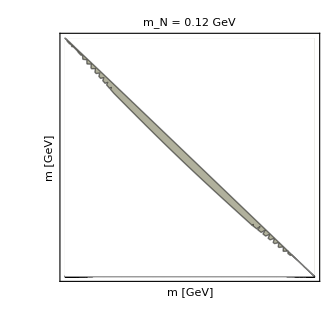
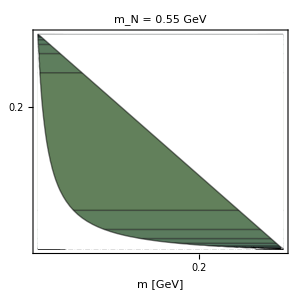
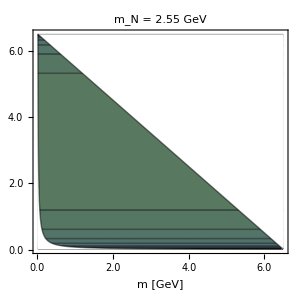
-Graphics--Graphics--Graphics--Graphics-

```mathematica
dalitzRescaleeμν=Style[Row[{dalitzTableeμν[[1]],dalitzTableeμν[[3]],dalitzTableeμν[[5]],cropVector[dalitzRescaleLeg,0.35,0.49,150,375] }],ImageSizeMultipliers-> 1,LineBreakWithin->False]
```

#### for μ mixing

```mathematica
minLog10Masseeν=Log10[2me];
maxLog10Masseeν=Log10[5];
```

```mathematica
ΓeeνMassTable=logspace[minLog10Masseeν,maxLog10Masseeν,bins];
```

```mathematica
Clear[dalitzRescaleTableeeν]
dalitzRescaleTableeeν=Table[reportColorRange[Evaluate[CleanContourPlot[ΓRescaleContourPlot[ΓeeνMassTable[[Round[((bins - 1)i)/5 ]+6]],me,me,0,AeeνSq,Γeeν,IntegerQ[i/3]]]]],{i,0,4}];
```

$Aborted

```mathematica
dalitzBoundaryTableeeν=Table[CleanContourPlot[boundaryContour[ΓeeνMassTable[[Round[((bins - 1)i)/5 ]+6]],me,me,0]],{i,0,4}];
```

```mathematica
dalitzTableeeν=Table[Show[dalitzRescaleTableeeν[[i,1]],dalitzBoundaryTableeeν[[i]]],{i,1,5}];
```

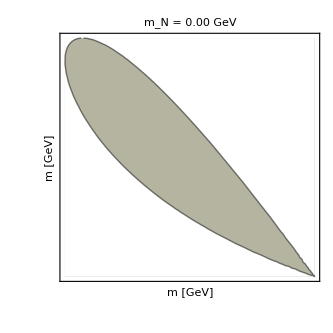
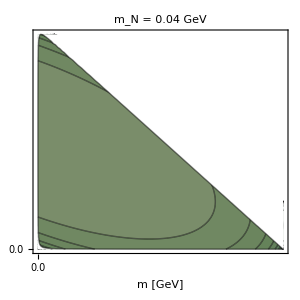
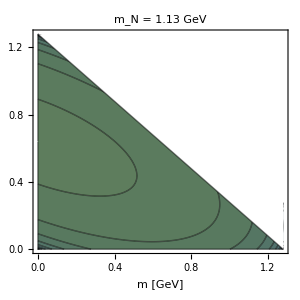
-Graphics--Graphics--Graphics--Graphics-

```mathematica
dalitzRescaleeeν=Style[Row[{dalitzTableeeν[[1]],dalitzTableeeν[[3]],dalitzTableeeν[[5]],cropVector[dalitzRescaleLeg,0.35,0.49,150,375] }],ImageSizeMultipliers-> 1,LineBreakWithin->False]
```

#### for e mixing

```mathematica
minLog10Massμμν=Log10[2mμ];
maxLog10Massμμν=Log10[5];
```

```mathematica
ΓμμνMassTable=logspace[minLog10Massμμν,maxLog10Massμμν,bins];
```

```mathematica
Clear[dalitzRescaleTable]
dalitzRescaleTable=Table[reportColorRange[Evaluate[CleanContourPlot[ΓRescaleContourPlot[ΓμμνMassTable[[Round[((bins - 1)i)/5 ]+6]],mμ,mμ,0,AμμνSq,Γμμν,IntegerQ[i/3],"e"]]]],{i,0,4}];
```

```mathematica
dalitzBoundaryTable=Table[CleanContourPlot[boundaryContour[ΓμμνMassTable[[Round[((bins - 1)i)/5 ]+6]],mμ,mμ,0]],{i,0,4}];
```

```mathematica
dalitzTable=Table[Show[dalitzRescaleTable[[i,1]],dalitzBoundaryTable[[i]]],{i,1,5}];
```

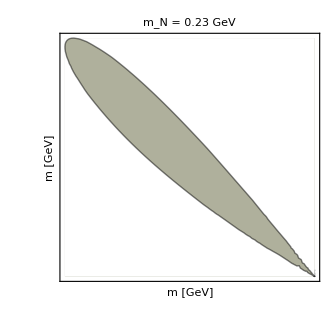
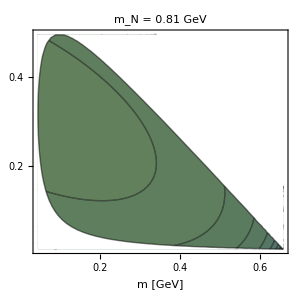
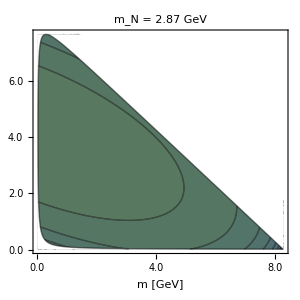
-Graphics--Graphics--Graphics--Graphics-

```mathematica
dalitzRescaleRow1=Style[Row[{dalitzTable[[1]],dalitzTable[[3]],dalitzTable[[5]],cropVector[dalitzRescaleLeg,0.35,0.49,150,375] }],ImageSizeMultipliers-> 1,LineBreakWithin->False]
```

## Export of Dalitz weights

### Export Function

```mathematica
OutDir = NotebookDirectory[];
```

```mathematica
MixingDict[Mixing_]:= Switch[Mixing,
"e", "El",
"μ", "Mu",
"τ","Tau"
];
FinalMassesDict[FinalState_,Mixing_]:=
Switch[FinalState,
"NuElMu",  {me,mμ,0},
"NuElEl", {me,me,0},
"NuMuMu", {mμ,mμ,0},
_,{0,0,0}
];
```

```mathematica
ExportDalitzWeights[FinalState_, Mixing_]:=Module[{ASq,Γ, FinalMasses,MassTable,output},
Γ[mN_]:=Switch[FinalState,
"NuElEl", Γeeν[mN,Mixing],
"NuMuMu", Γμμν[mN,Mixing],
"NuElMu", Γeμν[mN,Mixing]
];
ASq[mN_,m12sq_,m23sq_]:=Switch[FinalState,
"NuElEl", AeeνSq[mN,m12sq,m23sq,Mixing],
"NuMuMu", AμμνSq[mN,m12sq,m23sq,Mixing],
"NuElMu", AeμνSq[mN,m12sq,m23sq,Mixing]
];
FinalMasses =FinalMassesDict[FinalState,Mixing];
MassTable =Select[massList, #> Total[FinalMasses]&];
output=Flatten[ParallelTable[{Log10[mN],m12sq,m23sq,
If[Or[m23sq<M232min[m12sq,mN,FinalMasses[[1]],FinalMasses[[2]],FinalMasses[[3]]],M232max[m12sq,mN,FinalMasses[[1]],FinalMasses[[2]],FinalMasses[[3]]]<m23sq,
m12sq<(FinalMasses[[1]]+FinalMasses[[2]])^2, (mN-FinalMasses[[3]])^2<m12sq
],
0.,ASq[mN,m12sq,m23sq]/Γ[mN]]},
{mN,MassTable},{m12sq,linspace[(FinalMasses[[1]]+FinalMasses[[2]])^2+ϵ,(mN-FinalMasses[[3]])^2-ϵ,100]},{m23sq,linspace[(FinalMasses[[2]]+FinalMasses[[3]])^2+ϵ,(mN-FinalMasses[[1]])^2-ϵ,100]}],2]; 
Export[FileNameJoin[{OutDir,"Dalitz",StringJoin[FinalState,"-",MixingDict[Mixing],"Mixing.dat"]}],output];
];
```

### Running export

```mathematica
FinalStates = {"NuElEl","NuMuMu","NuElMu"};
Mixings = {"e","μ","τ"};
```

```mathematica
Do[
ExportDalitzWeights[FinalState,Mixing];,
{FinalState,FinalStates},{Mixing,Mixings}
]//AbsoluteTiming
```

{477.574,Null}